# SchubertPolynomials` Package

A package implementing Schubert, key, and Grothendieck polynomials, additional permutation methods, pipe dreams, and M-convexity.

## Loading the Package

If SchubertPolynomials.m is not in the same folder as this file, replace NotebookDirectory[] below by the (string) complete system path to the folder containing SchubertPolynomials.m

```mathematica
schubertpolynomialsdirectory=NotebookDirectory[];
If[!MemberQ[$Path,schubertpolynomialsdirectory],AppendTo[$Path,schubertpolynomialsdirectory]];
<<SchubertPolynomials.m;
```

## Permutations

Permutations are represented through either one-line notation as rearrangements of {1,2,...,n} or in cycle notation using the Mathematica Cycles[] function. All functions can accept either format. Use PermutationList and PermutationCycles to convert between the two.

```mathematica
w=RandomChoice[Permutations[5]]
u=Transposition[1,3]
v=Letter[2]
```

{2,5,4,1,3}

{3,2,1}

{1,3,2}

#### Common Permutation Functions

Descents and Inversions:

```mathematica
Descents[w]
Inversions[w]
```

{1,3}

{{1,2},{1,4},{1,5},{2,4},{3,4},{3,5}}

Lehmer Codes:

```mathematica
LehmerCode[w]
```

{3,1,2,0,0}

Rothe Diagrams and Rank Matrices:

{{1,1},{1,2},{1,3},{2,1},{3,1},{3,3}}

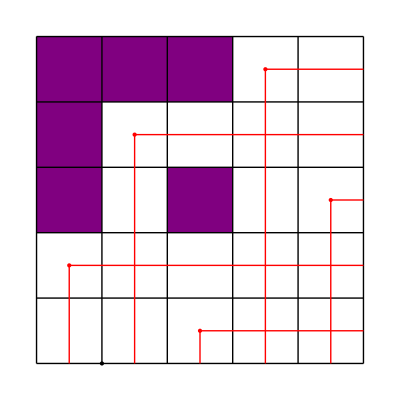

(0 | 0 | 0 | 1 | 1
0 | 1 | 1 | 2 | 2
0 | 1 | 1 | 2 | 3
1 | 2 | 2 | 3 | 4
1 | 2 | 3 | 4 | 5)

```mathematica
RotheDiagram[w]
DrawRotheDiagram[w]
RankMatrix[w]//MatrixForm
```

Inverses and Products (built in Mathematica functions compatible with the other functions in this package):

```mathematica
InversePermutation[w]
PermutationProduct[w,u]
```

{4,2,5,1,3}

{4,2,5,3,1}

Reduced Words:

```mathematica
ReducedWord[w]
ReducedWords[w]
```

{2,3,2,1,4,3}

{{2,3,2,1,4,3},{2,3,2,4,1,3},{2,3,2,4,3,1},{2,3,4,2,1,3},{2,3,4,2,3,1},{3,2,1,3,4,3},{3,2,1,4,3,4},{3,2,3,1,4,3},{3,2,3,4,1,3},{3,2,3,4,3,1},{3,2,4,1,3,4},{3,2,4,3,1,4},{3,2,4,3,4,1},{3,4,2,1,3,4},{3,4,2,3,1,4},{3,4,2,3,4,1}}

Wiring Diagrams:

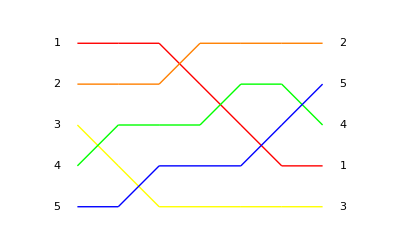

```mathematica
WiringDiagram[ReducedWord[w]]
```

Strong Bruhat Order:

```mathematica
BruhatOrderLessEqualQ[v,u]
BruhatOrderLessEqualCoverQ[u,w]
```

True

False

#### Common Permutation Class Tests

```mathematica
VexillaryQ[w]
GrassmannianQ[w]
DominantQ[w]
AvoidsPattern[w,v]
```

True

False

False

False

#### Pattern Avoidance Test

```mathematica
AvoidsPattern[w,v]
```

False

## Pipe Dreams

Pipe dreams are represented by matrices of zeros and ones, where a one is interpreted as a cross and a zero is interpreted as an elbow.

### Reduced and Non-reduced Pipe Dreams:

```mathematica
allPipes=PipeDreams[w];
reducedPipes=ReducedPipeDreams[w];
MatrixForm/@allPipes
MatrixForm/@reducedPipes
```

{(1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0),(1 | 0 | 0 | 1 | 0
1 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0),(1 | 0 | 0 | 1 | 0
1 | 1 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0),(1 | 0 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0),(1 | 0 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0),(1 | 0 | 1 | 1 | 0
1 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0),(1 | 0 | 1 | 1 | 0
1 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0),(1 | 0 | 1 | 1 | 0
1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0),(1 | 0 | 1 | 1 | 0
1 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0),(1 | 0 | 1 | 1 | 0
1 | 1 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0),(1 | 0 | 1 | 1 | 0
1 | 1 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)}

{(1 | 0 | 1 | 1 | 0
1 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0),(1 | 0 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0),(1 | 0 | 1 | 1 | 0
1 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0),(1 | 0 | 0 | 1 | 0
1 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)}

### Visualizing Pipe Dreams:

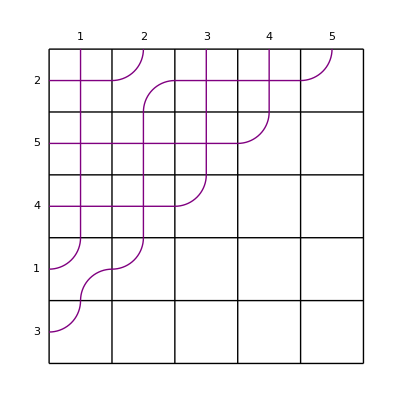

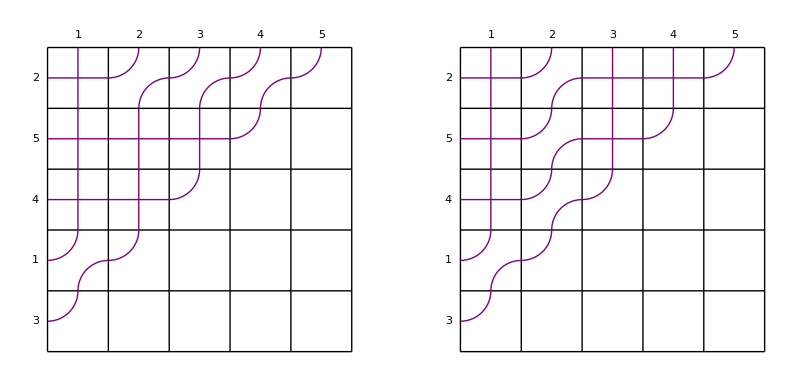

```mathematica
DrawPipeDream[allPipes[[-1]]]
GraphicsGrid[{{DrawPipeDream[BottomReducedPipeDream[w]],DrawPipeDream[TopReducedPipeDream[w]]}}]
```

## Schur, Schubert, Key, and Grothendieck Polynomials

### Computing Various Polynomials

The symbols x, y, t, and b are reserved for variables in this package.

Computing Schubert polynomials:

```mathematica
schub=SchubertPolynomial[w]
```

x[1]^3 x[2]^2 x[3]+x[1]^2 x[2]^3 x[3]+x[1]^3 x[2] x[3]^2+x[1]^2 x[2]^2 x[3]^2+x[1] x[2]^3 x[3]^2

Computing Schur polynomials:

```mathematica
lambda={4,3,1,0};
schur=SchurPolynomial[lambda]
```

x[1]^4 x[2]^3 x[3]+x[1]^3 x[2]^4 x[3]+x[1]^4 x[2]^2 x[3]^2+2 x[1]^3 x[2]^3 x[3]^2+x[1]^2 x[2]^4 x[3]^2+x[1]^4 x[2] x[3]^3+2 x[1]^3 x[2]^2 x[3]^3+2 x[1]^2 x[2]^3 x[3]^3+x[1] x[2]^4 x[3]^3+x[1]^3 x[2] x[3]^4+x[1]^2 x[2]^2 x[3]^4+x[1] x[2]^3 x[3]^4+x[1]^4 x[2]^3 x[4]+x[1]^3 x[2]^4 x[4]+2 x[1]^4 x[2]^2 x[3] x[4]+4 x[1]^3 x[2]^3 x[3] x[4]+2 x[1]^2 x[2]^4 x[3] x[4]+2 x[1]^4 x[2] x[3]^2 x[4]+5 x[1]^3 x[2]^2 x[3]^2 x[4]+5 x[1]^2 x[2]^3 x[3]^2 x[4]+2 x[1] x[2]^4 x[3]^2 x[4]+x[1]^4 x[3]^3 x[4]+4 x[1]^3 x[2] x[3]^3 x[4]+5 x[1]^2 x[2]^2 x[3]^3 x[4]+4 x[1] x[2]^3 x[3]^3 x[4]+x[2]^4 x[3]^3 x[4]+x[1]^3 x[3]^4 x[4]+2 x[1]^2 x[2] x[3]^4 x[4]+2 x[1] x[2]^2 x[3]^4 x[4]+x[2]^3 x[3]^4 x[4]+x[1]^4 x[2]^2 x[4]^2+2 x[1]^3 x[2]^3 x[4]^2+x[1]^2 x[2]^4 x[4]^2+2 x[1]^4 x[2] x[3] x[4]^2+5 x[1]^3 x[2]^2 x[3] x[4]^2+5 x[1]^2 x[2]^3 x[3] x[4]^2+2 x[1] x[2]^4 x[3] x[4]^2+x[1]^4 x[3]^2 x[4]^2+5 x[1]^3 x[2] x[3]^2 x[4]^2+7 x[1]^2 x[2]^2 x[3]^2 x[4]^2+5 x[1] x[2]^3 x[3]^2 x[4]^2+x[2]^4 x[3]^2 x[4]^2+2 x[1]^3 x[3]^3 x[4]^2+5 x[1]^2 x[2] x[3]^3 x[4]^2+5 x[1] x[2]^2 x[3]^3 x[4]^2+2 x[2]^3 x[3]^3 x[4]^2+x[1]^2 x[3]^4 x[4]^2+2 x[1] x[2] x[3]^4 x[4]^2+x[2]^2 x[3]^4 x[4]^2+x[1]^4 x[2] x[4]^3+2 x[1]^3 x[2]^2 x[4]^3+2 x[1]^2 x[2]^3 x[4]^3+x[1] x[2]^4 x[4]^3+x[1]^4 x[3] x[4]^3+4 x[1]^3 x[2] x[3] x[4]^3+5 x[1]^2 x[2]^2 x[3] x[4]^3+4 x[1] x[2]^3 x[3] x[4]^3+x[2]^4 x[3] x[4]^3+2 x[1]^3 x[3]^2 x[4]^3+5 x[1]^2 x[2] x[3]^2 x[4]^3+5 x[1] x[2]^2 x[3]^2 x[4]^3+2 x[2]^3 x[3]^2 x[4]^3+2 x[1]^2 x[3]^3 x[4]^3+4 x[1] x[2] x[3]^3 x[4]^3+2 x[2]^2 x[3]^3 x[4]^3+x[1] x[3]^4 x[4]^3+x[2] x[3]^4 x[4]^3+x[1]^3 x[2] x[4]^4+x[1]^2 x[2]^2 x[4]^4+x[1] x[2]^3 x[4]^4+x[1]^3 x[3] x[4]^4+2 x[1]^2 x[2] x[3] x[4]^4+2 x[1] x[2]^2 x[3] x[4]^4+x[2]^3 x[3] x[4]^4+x[1]^2 x[3]^2 x[4]^4+2 x[1] x[2] x[3]^2 x[4]^4+x[2]^2 x[3]^2 x[4]^4+x[1] x[3]^3 x[4]^4+x[2] x[3]^3 x[4]^4

Computing Key polynomials:

```mathematica
alpha={1,0,1,2};
key=KeyPolynomial[alpha]
```

x[1]^2 x[2] x[3]+x[1] x[2]^2 x[3]+x[1] x[2] x[3]^2+x[1]^2 x[2] x[4]+x[1] x[2]^2 x[4]+x[1]^2 x[3] x[4]+2 x[1] x[2] x[3] x[4]+x[1] x[3]^2 x[4]+x[1] x[2] x[4]^2+x[1] x[3] x[4]^2

Computing Grothendieck polynomials:

```mathematica
groth=GrothendieckPolynomial[w]
```

x[1]^3 x[2]^2 x[3]+x[1]^2 x[2]^3 x[3]-x[1]^3 x[2]^3 x[3]+x[1]^3 x[2] x[3]^2+x[1]^2 x[2]^2 x[3]^2-2 x[1]^3 x[2]^2 x[3]^2+x[1] x[2]^3 x[3]^2-2 x[1]^2 x[2]^3 x[3]^2+x[1]^3 x[2]^3 x[3]^2

Computing Double Schubert polynomials:

```mathematica
doubleschub=DoubleSchubertPolynomial[w]
```

x[1]^3 x[2]^2 x[3]+x[1]^2 x[2]^3 x[3]+x[1]^3 x[2] x[3]^2+x[1]^2 x[2]^2 x[3]^2+x[1] x[2]^3 x[3]^2-x[1]^3 x[2]^2 y[1]-x[1]^2 x[2]^3 y[1]-2 x[1]^3 x[2] x[3] y[1]-3 x[1]^2 x[2]^2 x[3] y[1]-2 x[1] x[2]^3 x[3] y[1]-x[1]^3 x[3]^2 y[1]-2 x[1]^2 x[2] x[3]^2 y[1]-2 x[1] x[2]^2 x[3]^2 y[1]-x[2]^3 x[3]^2 y[1]+x[1]^3 x[2] y[1]^2+2 x[1]^2 x[2]^2 y[1]^2+x[1] x[2]^3 y[1]^2+x[1]^3 x[3] y[1]^2+3 x[1]^2 x[2] x[3] y[1]^2+3 x[1] x[2]^2 x[3] y[1]^2+x[2]^3 x[3] y[1]^2+x[1]^2 x[3]^2 y[1]^2+x[1] x[2] x[3]^2 y[1]^2+x[2]^2 x[3]^2 y[1]^2-x[1]^2 x[2] y[1]^3-x[1] x[2]^2 y[1]^3-x[1]^2 x[3] y[1]^3-x[1] x[2] x[3] y[1]^3-x[2]^2 x[3] y[1]^3-x[1]^3 x[2] x[3] y[2]-2 x[1]^2 x[2]^2 x[3] y[2]-x[1] x[2]^3 x[3] y[2]-x[1]^2 x[2] x[3]^2 y[2]-x[1] x[2]^2 x[3]^2 y[2]+x[1]^3 x[2] y[1] y[2]+2 x[1]^2 x[2]^2 y[1] y[2]+x[1] x[2]^3 y[1] y[2]+x[1]^3 x[3] y[1] y[2]+4 x[1]^2 x[2] x[3] y[1] y[2]+4 x[1] x[2]^2 x[3] y[1] y[2]+x[2]^3 x[3] y[1] y[2]+x[1]^2 x[3]^2 y[1] y[2]+2 x[1] x[2] x[3]^2 y[1] y[2]+x[2]^2 x[3]^2 y[1] y[2]-x[1]^3 y[1]^2 y[2]-3 x[1]^2 x[2] y[1]^2 y[2]-3 x[1] x[2]^2 y[1]^2 y[2]-x[2]^3 y[1]^2 y[2]-2 x[1]^2 x[3] y[1]^2 y[2]-4 x[1] x[2] x[3] y[1]^2 y[2]-2 x[2]^2 x[3] y[1]^2 y[2]-x[1] x[3]^2 y[1]^2 y[2]-x[2] x[3]^2 y[1]^2 y[2]+x[1]^2 y[1]^3 y[2]+2 x[1] x[2] y[1]^3 y[2]+x[2]^2 y[1]^3 y[2]+x[1] x[3] y[1]^3 y[2]+x[2] x[3] y[1]^3 y[2]+x[1]^2 x[2] x[3] y[2]^2+x[1] x[2]^2 x[3] y[2]^2-x[1]^2 x[2] y[1] y[2]^2-x[1] x[2]^2 y[1] y[2]^2-x[1]^2 x[3] y[1] y[2]^2-2 x[1] x[2] x[3] y[1] y[2]^2-x[2]^2 x[3] y[1] y[2]^2+x[1]^2 y[1]^2 y[2]^2+2 x[1] x[2] y[1]^2 y[2]^2+x[2]^2 y[1]^2 y[2]^2+x[1] x[3] y[1]^2 y[2]^2+x[2] x[3] y[1]^2 y[2]^2-x[1] y[1]^3 y[2]^2-x[2] y[1]^3 y[2]^2-x[1]^3 x[2] x[3] y[3]-2 x[1]^2 x[2]^2 x[3] y[3]-x[1] x[2]^3 x[3] y[3]-x[1]^2 x[2] x[3]^2 y[3]-x[1] x[2]^2 x[3]^2 y[3]+x[1]^3 x[2] y[1] y[3]+2 x[1]^2 x[2]^2 y[1] y[3]+x[1] x[2]^3 y[1] y[3]+x[1]^3 x[3] y[1] y[3]+4 x[1]^2 x[2] x[3] y[1] y[3]+4 x[1] x[2]^2 x[3] y[1] y[3]+x[2]^3 x[3] y[1] y[3]+x[1]^2 x[3]^2 y[1] y[3]+2 x[1] x[2] x[3]^2 y[1] y[3]+x[2]^2 x[3]^2 y[1] y[3]-x[1]^3 y[1]^2 y[3]-3 x[1]^2 x[2] y[1]^2 y[3]-3 x[1] x[2]^2 y[1]^2 y[3]-x[2]^3 y[1]^2 y[3]-2 x[1]^2 x[3] y[1]^2 y[3]-4 x[1] x[2] x[3] y[1]^2 y[3]-2 x[2]^2 x[3] y[1]^2 y[3]-x[1] x[3]^2 y[1]^2 y[3]-x[2] x[3]^2 y[1]^2 y[3]+x[1]^2 y[1]^3 y[3]+2 x[1] x[2] y[1]^3 y[3]+x[2]^2 y[1]^3 y[3]+x[1] x[3] y[1]^3 y[3]+x[2] x[3] y[1]^3 y[3]+2 x[1]^2 x[2] x[3] y[2] y[3]+2 x[1] x[2]^2 x[3] y[2] y[3]+x[1] x[2] x[3]^2 y[2] y[3]-2 x[1]^2 x[2] y[1] y[2] y[3]-2 x[1] x[2]^2 y[1] y[2] y[3]-2 x[1]^2 x[3] y[1] y[2] y[3]-5 x[1] x[2] x[3] y[1] y[2] y[3]-2 x[2]^2 x[3] y[1] y[2] y[3]-x[1] x[3]^2 y[1] y[2] y[3]-x[2] x[3]^2 y[1] y[2] y[3]+2 x[1]^2 y[1]^2 y[2] y[3]+4 x[1] x[2] y[1]^2 y[2] y[3]+2 x[2]^2 y[1]^2 y[2] y[3]+3 x[1] x[3] y[1]^2 y[2] y[3]+3 x[2] x[3] y[1]^2 y[2] y[3]+x[3]^2 y[1]^2 y[2] y[3]-2 x[1] y[1]^3 y[2] y[3]-2 x[2] y[1]^3 y[2] y[3]-x[3] y[1]^3 y[2] y[3]-x[1] x[2] x[3] y[2]^2 y[3]+x[1] x[2] y[1] y[2]^2 y[3]+x[1] x[3] y[1] y[2]^2 y[3]+x[2] x[3] y[1] y[2]^2 y[3]-x[1] y[1]^2 y[2]^2 y[3]-x[2] y[1]^2 y[2]^2 y[3]-x[3] y[1]^2 y[2]^2 y[3]+y[1]^3 y[2]^2 y[3]+x[1]^2 x[2] x[3] y[3]^2+x[1] x[2]^2 x[3] y[3]^2-x[1]^2 x[2] y[1] y[3]^2-x[1] x[2]^2 y[1] y[3]^2-x[1]^2 x[3] y[1] y[3]^2-2 x[1] x[2] x[3] y[1] y[3]^2-x[2]^2 x[3] y[1] y[3]^2+x[1]^2 y[1]^2 y[3]^2+2 x[1] x[2] y[1]^2 y[3]^2+x[2]^2 y[1]^2 y[3]^2+x[1] x[3] y[1]^2 y[3]^2+x[2] x[3] y[1]^2 y[3]^2-x[1] y[1]^3 y[3]^2-x[2] y[1]^3 y[3]^2-x[1] x[2] x[3] y[2] y[3]^2+x[1] x[2] y[1] y[2] y[3]^2+x[1] x[3] y[1] y[2] y[3]^2+x[2] x[3] y[1] y[2] y[3]^2-x[1] y[1]^2 y[2] y[3]^2-x[2] y[1]^2 y[2] y[3]^2-x[3] y[1]^2 y[2] y[3]^2+y[1]^3 y[2] y[3]^2-x[1]^2 x[2]^2 x[3] y[4]-x[1]^2 x[2] x[3]^2 y[4]-x[1] x[2]^2 x[3]^2 y[4]+x[1]^2 x[2]^2 y[1] y[4]+2 x[1]^2 x[2] x[3] y[1] y[4]+2 x[1] x[2]^2 x[3] y[1] y[4]+x[1]^2 x[3]^2 y[1] y[4]+2 x[1] x[2] x[3]^2 y[1] y[4]+x[2]^2 x[3]^2 y[1] y[4]-x[1]^2 x[2] y[1]^2 y[4]-x[1] x[2]^2 y[1]^2 y[4]-x[1]^2 x[3] y[1]^2 y[4]-3 x[1] x[2] x[3] y[1]^2 y[4]-x[2]^2 x[3] y[1]^2 y[4]-x[1] x[3]^2 y[1]^2 y[4]-x[2] x[3]^2 y[1]^2 y[4]+x[1] x[2] y[1]^3 y[4]+x[1] x[3] y[1]^3 y[4]+x[2] x[3] y[1]^3 y[4]+x[1]^2 x[2] x[3] y[2] y[4]+x[1] x[2]^2 x[3] y[2] y[4]+x[1] x[2] x[3]^2 y[2] y[4]-x[1]^2 x[2] y[1] y[2] y[4]-x[1] x[2]^2 y[1] y[2] y[4]-x[1]^2 x[3] y[1] y[2] y[4]-3 x[1] x[2] x[3] y[1] y[2] y[4]-x[2]^2 x[3] y[1] y[2] y[4]-x[1] x[3]^2 y[1] y[2] y[4]-x[2] x[3]^2 y[1] y[2] y[4]+x[1]^2 y[1]^2 y[2] y[4]+2 x[1] x[2] y[1]^2 y[2] y[4]+x[2]^2 y[1]^2 y[2] y[4]+2 x[1] x[3] y[1]^2 y[2] y[4]+2 x[2] x[3] y[1]^2 y[2] y[4]+x[3]^2 y[1]^2 y[2] y[4]-x[1] y[1]^3 y[2] y[4]-x[2] y[1]^3 y[2] y[4]-x[3] y[1]^3 y[2] y[4]-x[1] x[2] x[3] y[2]^2 y[4]+x[1] x[2] y[1] y[2]^2 y[4]+x[1] x[3] y[1] y[2]^2 y[4]+x[2] x[3] y[1] y[2]^2 y[4]-x[1] y[1]^2 y[2]^2 y[4]-x[2] y[1]^2 y[2]^2 y[4]-x[3] y[1]^2 y[2]^2 y[4]+y[1]^3 y[2]^2 y[4]+x[1]^2 x[2] x[3] y[3] y[4]+x[1] x[2]^2 x[3] y[3] y[4]+x[1] x[2] x[3]^2 y[3] y[4]-x[1]^2 x[2] y[1] y[3] y[4]-x[1] x[2]^2 y[1] y[3] y[4]-x[1]^2 x[3] y[1] y[3] y[4]-3 x[1] x[2] x[3] y[1] y[3] y[4]-x[2]^2 x[3] y[1] y[3] y[4]-x[1] x[3]^2 y[1] y[3] y[4]-x[2] x[3]^2 y[1] y[3] y[4]+x[1]^2 y[1]^2 y[3] y[4]+2 x[1] x[2] y[1]^2 y[3] y[4]+x[2]^2 y[1]^2 y[3] y[4]+2 x[1] x[3] y[1]^2 y[3] y[4]+2 x[2] x[3] y[1]^2 y[3] y[4]+x[3]^2 y[1]^2 y[3] y[4]-x[1] y[1]^3 y[3] y[4]-x[2] y[1]^3 y[3] y[4]-x[3] y[1]^3 y[3] y[4]-x[1] x[2] x[3] y[2] y[3] y[4]+x[1] x[2] y[1] y[2] y[3] y[4]+x[1] x[3] y[1] y[2] y[3] y[4]+x[2] x[3] y[1] y[2] y[3] y[4]-x[1] y[1]^2 y[2] y[3] y[4]-x[2] y[1]^2 y[2] y[3] y[4]-x[3] y[1]^2 y[2] y[3] y[4]+y[1]^3 y[2] y[3] y[4]-x[1] x[2] x[3] y[3]^2 y[4]+x[1] x[2] y[1] y[3]^2 y[4]+x[1] x[3] y[1] y[3]^2 y[4]+x[2] x[3] y[1] y[3]^2 y[4]-x[1] y[1]^2 y[3]^2 y[4]-x[2] y[1]^2 y[3]^2 y[4]-x[3] y[1]^2 y[3]^2 y[4]+y[1]^3 y[3]^2 y[4]

Computing Double Grothendieck polynomials:

```mathematica
doublegroth=DoubleGrothendieckPolynomial[w]
```

x[1]^3 x[2]^2 x[3]+x[1]^2 x[2]^3 x[3]-x[1]^3 x[2]^3 x[3]+x[1]^3 x[2] x[3]^2+x[1]^2 x[2]^2 x[3]^2-2 x[1]^3 x[2]^2 x[3]^2+3739+9 x[1]^2 x[2]^2 x[3]^2 y[1]^3 y[2]^2 y[3]^2 y[4]-3 x[1]^3 x[2]^2 x[3]^2 y[1]^3 y[2]^2 y[3]^2 y[4]-x[2]^3 x[3]^2 y[1]^3 y[2]^2 y[3]^2 y[4]+3 x[1] x[2]^3 x[3]^2 y[1]^3 y[2]^2 y[3]^2 y[4]-3 x[1]^2 x[2]^3 x[3]^2 y[1]^3 y[2]^2 y[3]^2 y[4]+x[1]^3 x[2]^3 x[3]^2 y[1]^3 y[2]^2 y[3]^2 y[4]
 |  |  |  |

#### Working With Polynomials

Shorthand for common variable lists:

```mathematica
w
XVariables[w]
XYVariables[w]
XVariables[4]
```

{2,5,4,1,3}

{x[1],x[2],x[3],x[4]}

{x[1],x[2],x[3],x[4],y[1],y[2],y[3],y[4]}

{x[1],x[2],x[3],x[4]}

Extracting Exponents:

```mathematica
schubexps=Exponents[schub,XVariables[w]]
keyexps=Exponents[key,Array[x,Length[alpha]]]
grothexps=Exponents[groth,XVariables[w]]
doubleschubexps=Exponents[doubleschub,XYVariables[w]]
```

{{3,2,1,0},{3,1,2,0},{2,3,1,0},{2,2,2,0},{1,3,2,0}}

{{2,1,1,0},{2,1,0,1},{2,0,1,1},{1,2,1,0},{1,2,0,1},{1,1,2,0},{1,1,1,1},{1,1,0,2},{1,0,2,1},{1,0,1,2}}

{{3,3,2,0},{3,3,1,0},{3,2,2,0},{3,2,1,0},{3,1,2,0},{2,3,2,0},{2,3,1,0},{2,2,2,0},{1,3,2,0}}

{{3,2,1,0,0,0,0,0},{3,2,0,0,1,0,0,0},{3,1,2,0,0,0,0,0},{3,1,1,0,1,0,0,0},{3,1,1,0,0,1,0,0},{3,1,1,0,0,0,1,0},{3,1,0,0,2,0,0,0},{3,1,0,0,1,1,0,0},{3,1,0,0,1,0,1,0},{3,0,2,0,1,0,0,0},{3,0,1,0,2,0,0,0},{3,0,1,0,1,1,0,0},{3,0,1,0,1,0,1,0},{3,0,0,0,2,1,0,0},{3,0,0,0,2,0,1,0},{2,3,1,0,0,0,0,0},{2,3,0,0,1,0,0,0},{2,2,2,0,0,0,0,0},{2,2,1,0,1,0,0,0},{2,2,1,0,0,1,0,0},{2,2,1,0,0,0,1,0},{2,2,1,0,0,0,0,1},{2,2,0,0,2,0,0,0},{2,2,0,0,1,1,0,0},{2,2,0,0,1,0,1,0},{2,2,0,0,1,0,0,1},{2,1,2,0,1,0,0,0},{2,1,2,0,0,1,0,0},{2,1,2,0,0,0,1,0},{2,1,2,0,0,0,0,1},{2,1,1,0,2,0,0,0},{2,1,1,0,1,1,0,0},{2,1,1,0,1,0,1,0},{2,1,1,0,1,0,0,1},{2,1,1,0,0,2,0,0},{2,1,1,0,0,1,1,0},{2,1,1,0,0,1,0,1},{2,1,1,0,0,0,2,0},{2,1,1,0,0,0,1,1},{2,1,0,0,3,0,0,0},{2,1,0,0,2,1,0,0},{2,1,0,0,2,0,1,0},{2,1,0,0,2,0,0,1},{2,1,0,0,1,2,0,0},{2,1,0,0,1,1,1,0},{2,1,0,0,1,1,0,1},{2,1,0,0,1,0,2,0},{2,1,0,0,1,0,1,1},{2,0,2,0,2,0,0,0},{2,0,2,0,1,1,0,0},{2,0,2,0,1,0,1,0},{2,0,2,0,1,0,0,1},{2,0,1,0,3,0,0,0},{2,0,1,0,2,1,0,0},{2,0,1,0,2,0,1,0},{2,0,1,0,2,0,0,1},{2,0,1,0,1,2,0,0},{2,0,1,0,1,1,1,0},{2,0,1,0,1,1,0,1},{2,0,1,0,1,0,2,0},{2,0,1,0,1,0,1,1},{2,0,0,0,3,1,0,0},{2,0,0,0,3,0,1,0},{2,0,0,0,2,2,0,0},{2,0,0,0,2,1,1,0},{2,0,0,0,2,1,0,1},{2,0,0,0,2,0,2,0},{2,0,0,0,2,0,1,1},{1,3,2,0,0,0,0,0},{1,3,1,0,1,0,0,0},{1,3,1,0,0,1,0,0},{1,3,1,0,0,0,1,0},{1,3,0,0,2,0,0,0},{1,3,0,0,1,1,0,0},{1,3,0,0,1,0,1,0},{1,2,2,0,1,0,0,0},{1,2,2,0,0,1,0,0},{1,2,2,0,0,0,1,0},{1,2,2,0,0,0,0,1},{1,2,1,0,2,0,0,0},{1,2,1,0,1,1,0,0},{1,2,1,0,1,0,1,0},{1,2,1,0,1,0,0,1},{1,2,1,0,0,2,0,0},{1,2,1,0,0,1,1,0},{1,2,1,0,0,1,0,1},{1,2,1,0,0,0,2,0},{1,2,1,0,0,0,1,1},{1,2,0,0,3,0,0,0},{1,2,0,0,2,1,0,0},{1,2,0,0,2,0,1,0},{1,2,0,0,2,0,0,1},{1,2,0,0,1,2,0,0},{1,2,0,0,1,1,1,0},{1,2,0,0,1,1,0,1},{1,2,0,0,1,0,2,0},{1,2,0,0,1,0,1,1},{1,1,2,0,2,0,0,0},{1,1,2,0,1,1,0,0},{1,1,2,0,1,0,1,0},{1,1,2,0,1,0,0,1},{1,1,2,0,0,1,1,0},{1,1,2,0,0,1,0,1},{1,1,2,0,0,0,1,1},{1,1,1,0,3,0,0,0},{1,1,1,0,2,1,0,0},{1,1,1,0,2,0,1,0},{1,1,1,0,2,0,0,1},{1,1,1,0,1,2,0,0},{1,1,1,0,1,1,1,0},{1,1,1,0,1,1,0,1},{1,1,1,0,1,0,2,0},{1,1,1,0,1,0,1,1},{1,1,1,0,0,2,1,0},{1,1,1,0,0,2,0,1},{1,1,1,0,0,1,2,0},{1,1,1,0,0,1,1,1},{1,1,1,0,0,0,2,1},{1,1,0,0,3,1,0,0},{1,1,0,0,3,0,1,0},{1,1,0,0,3,0,0,1},{1,1,0,0,2,2,0,0},{1,1,0,0,2,1,1,0},{1,1,0,0,2,1,0,1},{1,1,0,0,2,0,2,0},{1,1,0,0,2,0,1,1},{1,1,0,0,1,2,1,0},{1,1,0,0,1,2,0,1},{1,1,0,0,1,1,2,0},{1,1,0,0,1,1,1,1},{1,1,0,0,1,0,2,1},{1,0,2,0,2,1,0,0},{1,0,2,0,2,0,1,0},{1,0,2,0,2,0,0,1},{1,0,2,0,1,1,1,0},{1,0,2,0,1,1,0,1},{1,0,2,0,1,0,1,1},{1,0,1,0,3,1,0,0},{1,0,1,0,3,0,1,0},{1,0,1,0,3,0,0,1},{1,0,1,0,2,2,0,0},{1,0,1,0,2,1,1,0},{1,0,1,0,2,1,0,1},{1,0,1,0,2,0,2,0},{1,0,1,0,2,0,1,1},{1,0,1,0,1,2,1,0},{1,0,1,0,1,2,0,1},{1,0,1,0,1,1,2,0},{1,0,1,0,1,1,1,1},{1,0,1,0,1,0,2,1},{1,0,0,0,3,2,0,0},{1,0,0,0,3,1,1,0},{1,0,0,0,3,1,0,1},{1,0,0,0,3,0,2,0},{1,0,0,0,3,0,1,1},{1,0,0,0,2,2,1,0},{1,0,0,0,2,2,0,1},{1,0,0,0,2,1,2,0},{1,0,0,0,2,1,1,1},{1,0,0,0,2,0,2,1},{0,3,2,0,1,0,0,0},{0,3,1,0,2,0,0,0},{0,3,1,0,1,1,0,0},{0,3,1,0,1,0,1,0},{0,3,0,0,2,1,0,0},{0,3,0,0,2,0,1,0},{0,2,2,0,2,0,0,0},{0,2,2,0,1,1,0,0},{0,2,2,0,1,0,1,0},{0,2,2,0,1,0,0,1},{0,2,1,0,3,0,0,0},{0,2,1,0,2,1,0,0},{0,2,1,0,2,0,1,0},{0,2,1,0,2,0,0,1},{0,2,1,0,1,2,0,0},{0,2,1,0,1,1,1,0},{0,2,1,0,1,1,0,1},{0,2,1,0,1,0,2,0},{0,2,1,0,1,0,1,1},{0,2,0,0,3,1,0,0},{0,2,0,0,3,0,1,0},{0,2,0,0,2,2,0,0},{0,2,0,0,2,1,1,0},{0,2,0,0,2,1,0,1},{0,2,0,0,2,0,2,0},{0,2,0,0,2,0,1,1},{0,1,2,0,2,1,0,0},{0,1,2,0,2,0,1,0},{0,1,2,0,2,0,0,1},{0,1,2,0,1,1,1,0},{0,1,2,0,1,1,0,1},{0,1,2,0,1,0,1,1},{0,1,1,0,3,1,0,0},{0,1,1,0,3,0,1,0},{0,1,1,0,3,0,0,1},{0,1,1,0,2,2,0,0},{0,1,1,0,2,1,1,0},{0,1,1,0,2,1,0,1},{0,1,1,0,2,0,2,0},{0,1,1,0,2,0,1,1},{0,1,1,0,1,2,1,0},{0,1,1,0,1,2,0,1},{0,1,1,0,1,1,2,0},{0,1,1,0,1,1,1,1},{0,1,1,0,1,0,2,1},{0,1,0,0,3,2,0,0},{0,1,0,0,3,1,1,0},{0,1,0,0,3,1,0,1},{0,1,0,0,3,0,2,0},{0,1,0,0,3,0,1,1},{0,1,0,0,2,2,1,0},{0,1,0,0,2,2,0,1},{0,1,0,0,2,1,2,0},{0,1,0,0,2,1,1,1},{0,1,0,0,2,0,2,1},{0,0,2,0,2,1,1,0},{0,0,2,0,2,1,0,1},{0,0,2,0,2,0,1,1},{0,0,1,0,3,1,1,0},{0,0,1,0,3,1,0,1},{0,0,1,0,3,0,1,1},{0,0,1,0,2,2,1,0},{0,0,1,0,2,2,0,1},{0,0,1,0,2,1,2,0},{0,0,1,0,2,1,1,1},{0,0,1,0,2,0,2,1},{0,0,0,0,3,2,1,0},{0,0,0,0,3,2,0,1},{0,0,0,0,3,1,2,0},{0,0,0,0,3,1,1,1},{0,0,0,0,3,0,2,1}}

Extracting Coefficients:

```mathematica
schubcoeffs=Coefficients[schub,XVariables[w]]
grothcoeffs=Coefficients[groth,XVariables[w]]
doubleschubcoeffs=Coefficients[doubleschub,XYVariables[w]]
```

{1,1,1,1,1}

{1,-1,-2,1,1,-2,1,1,1}

{1,-1,1,-2,-1,-1,1,1,1,-1,1,1,1,-1,-1,1,-1,1,-3,-2,-2,-1,2,2,2,1,-2,-1,-1,-1,3,4,4,2,1,2,1,1,1,-1,-3,-3,-1,-1,-2,-1,-1,-1,1,1,1,1,-1,-2,-2,-1,-1,-2,-1,-1,-1,1,1,1,2,1,1,1,1,-2,-1,-1,1,1,1,-2,-1,-1,-1,3,4,4,2,1,2,1,1,1,-1,-3,-3,-1,-1,-2,-1,-1,-1,1,2,2,2,1,1,1,-1,-4,-4,-3,-2,-5,-3,-2,-3,-1,-1,-1,-1,-1,2,2,1,2,4,2,2,2,1,1,1,1,1,-1,-1,-1,-1,-1,-1,1,1,1,1,3,2,1,2,1,1,1,1,1,-1,-2,-1,-1,-1,-1,-1,-1,-1,-1,-1,1,1,1,-1,-1,1,1,1,1,-1,-2,-2,-1,-1,-2,-1,-1,-1,1,1,1,2,1,1,1,-1,-1,-1,-1,-1,-1,1,1,1,1,3,2,1,2,1,1,1,1,1,-1,-2,-1,-1,-1,-1,-1,-1,-1,-1,1,1,1,-1,-1,-1,-1,-1,-1,-1,-1,1,1,1,1,1}

Extracting Homogeneous Components:

```mathematica
HomogeneousComponents[groth,XVariables[w]]
```

{x[1]^3 x[2]^2 x[3]+x[1]^2 x[2]^3 x[3]+x[1]^3 x[2] x[3]^2+x[1]^2 x[2]^2 x[3]^2+x[1] x[2]^3 x[3]^2,-x[1]^3 x[2]^3 x[3]-2 x[1]^3 x[2]^2 x[3]^2-2 x[1]^2 x[2]^3 x[3]^2,x[1]^3 x[2]^3 x[3]^2}

## M-Convexity and Lorentzian Polynomials

Checking if a list of integer points is an M-convex set, that is the set of integral points of an integral generalized permutahedron:

```mathematica
MConvexSetQ[schubexps]
MConvexSetQ[doubleschubexps]
MConvexSetQ/@(Exponents[#,XVariables[w]]&/@HomogeneousComponents[groth,XVariables[w]])
```

True

True

{True,True,True}

Checking if a polynomial is Lorentzian.

```mathematica
normschub=NormalizePolynomial[schub];
LorentzianPolynomialQ[normschub]
```

True